# Serienschwingkreis

## Funktionen

### Includes

```mathematica
<<"Labor.m"
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"]
Gauss[a_]:= Module[{},{Mean[a],StandardDeviation[a]/Sqrt[Length[a]]}];
```

## Geräteliste

Oszi:
true rms:

## 1.) Resonanzfrequenz (Bestimmung aus Phasenverlauf am Widerstand)

### Induktivität und Kapazität

```mathematica
l={5.6,0}*10^-3;
rl=0.83;
c={0.15,0.01}*10^-6;
r={10,0};
r2 = {50,0};
```

### Theoretische Resonanzfrequenz

```mathematica
f0=(Elec`Fω[l[[1]],l[[2]],c[[1]],c[[2]]])/(2*π)
```

{5491.37,183.046}

### Frequenzverteilung

```mathematica
f=Join[Table[f0[[1]]-f0[[1]]*10^Log[x/6],{x,1,6}],{f0[[1]]}];
f = Join[f,Table[f0[[1]]+f0[[1]]*10^Log[x/6],{x,1,6}]]//Sort
```

{0.,1882.6,3332.55,4378.27,5053.78,5402.67,5491.37,5580.07,5928.96,6604.46,7650.18,9100.13,10982.7}

### Theroretische Güte Q

```mathematica
Elec`FQ[r[[1]],r[[2]],l[[1]],l[[2]],c[[1]],c[[2]]]
```

{5.52052,0.184017}

```mathematica
Elec`FQ[r2[[1]],r2[[0]],l[[1]],l[[2]],c[[1]],c[[2]]]
```

{2.57624,0.0858748+0.0343499 List}

```mathematica
Begin["R`"];
```

### Messung (Achtung! Konstante Eingangsspannung von 2 V Spitze-Spitze, manuell nachregeln!)

```mathematica
{{N, "f/Hz", "Δf/Hz", "Ua/V", "ΔUa/V", "δt", "Δδt"}, {1, 1906, 1, 1.4*2*20*10^-3, 5*10^-3, 1.4*0.1*10^-3, 0.02*10^-3}, {2, 3349, 1, 1.4*2*50*10^-3, 10*10^-3, 1.4*50*10^-6, 10*10^-6}, {3, 4440, 1, 1.6*2*0.1, 0.02, 0.9*50*10^-6, 10*10^-6}, {4, 5000, 1, 1.6*2*0.2, 0.04, 0.5*50*10^-6, 10*10^-6}, {5, 5410, 1, 2*2*0.2, 0.04, 0.5*5*10^-6, 1*10^-6}, {6, 5491, 1, 2*2*0.2, 0.04, -0.6*10*10^-6, 2*10^-6}, {7, 5580, 1, 1.8*2*0.2, 0.04, -1.2*10*10^-6, 2*10^-6}, {8, 5.93*10^3, 10, 1.3*2*0.2, 0.04, -1.1*20*10^-6, 4*10^-6}, {9, 6.60*10^3, 10, 0.8*2*0.2, 0.04, -1.3*20*10^-6, 4*10^-6}, {10, 7.63*10^3, 10, 0.9*2*0.1, 0.02, -1.3*20*10^-6, 4*10^-6}, {11, 9.10*10^3, 10, 1.1*2*50*10^-3, 10*10^-3, -1.1*20*10^-6, 4*10^-6}, {12, 11.00*10^3, 10, 0.9*2*50*10^-3, 10*10^-3, -1*20*10^-6, 4*10^-6}, {13, 30.22*10^3, 10, 0.7*2*20*10^-3, 5*10^-3, -1.4*5*10^-6, 10^-6}}//TableForm//N
```

N | f/Hz | Δf/Hz | Ua/V | ΔUa/V | δt | Δδt
1. | 1906. | 1. | 0.056 | 0.005 | 0.00014 | 0.00002
2. | 3349. | 1. | 0.14 | 0.01 | 0.00007 | 0.00001
3. | 4440. | 1. | 0.32 | 0.02 | 0.000045 | 0.00001
4. | 5000. | 1. | 0.64 | 0.04 | 0.000025 | 0.00001
5. | 5410. | 1. | 0.8 | 0.04 | 2.5×10^-6 | 1.×10^-6
6. | 5491. | 1. | 0.8 | 0.04 | -6.×10^-6 | 2.×10^-6
7. | 5580. | 1. | 0.72 | 0.04 | -0.000012 | 2.×10^-6
8. | 5930. | 10. | 0.52 | 0.04 | -0.000022 | 4.×10^-6
9. | 6600. | 10. | 0.32 | 0.04 | -0.000026 | 4.×10^-6
10. | 7630. | 10. | 0.18 | 0.02 | -0.000026 | 4.×10^-6
11. | 9100. | 10. | 0.11 | 0.01 | -0.000022 | 4.×10^-6
12. | 11000. | 10. | 0.09 | 0.01 | -0.00002 | 4.×10^-6
13. | 30220. | 10. | 0.028 | 0.005 | -7.×10^-6 | 1.×10^-6

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {1906, 1.4*2*20*10^-3, 1.4*0.1*10^-3, 4*0.5}, {3349, 1.4*2*50*10^-3, 1.4*50*10^-6, 4*0.5}, {4440, 1.6*2*0.1, 0.9*50*10^-6, 4*0.5}, {5000, 1.6*2*0.2, 0.5*50*10^-6, 4*0.5}, {5410, 2*2*0.2, 0.5*5*10^-6, 4*0.5}, {5491, 2*2*0.2, -0.6*10*10^-6, 4*0.5}, {5580, 1.8*2*0.2, -1.2*10*10^-6, 4*0.5}, {5.93*10^3, 1.3*2*0.2, -1.1*20*10^-6, 4*0.5}, {6.60*10^3, 0.8*2*0.2, -1.3*20*10^-6, 4*0.5}, {7.63*10^3, 0.9*2*0.1, -1.3*20*10^-6, 4*0.5}, {9.10*10^3, 1.1*2*50*10^-3, -1.1*20*10^-6, 4*0.5}, {11.00*10^3, 0.9*2*50*10^-3, -1*20*10^-6, 4*0.5}, {30.22*10^3, 0.7*2*20*10^-3, -1.4*5*10^-6, 4*0.5}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {1, 5*10^-3, 0.02*10^-3, 0.1}, {1, 10*10^-3, 10*10^-6, 0.1}, {1, 0.02, 10*10^-6, 0.1}, {1, 0.04, 10*10^-6, 0.1}, {1, 0.04, 1*10^-6, 0.1}, {1, 0.04, 2*10^-6, 0.1}, {1, 0.04, 2*10^-6, 0.1}, {10, 0.04, 4*10^-6, 0.1}, {10, 0.04, 4*10^-6, 0.1}, {10, 0.02, 4*10^-6, 0.1}, {10, 10*10^-3, 4*10^-6, 0.1}, {10, 10*10^-3, 4*10^-6, 0.1}, {10, 5*10^-3, 10^-6, 0.1}};

Ue=4;(*eff, fluke 175*)
due=0.1;
```

### Amplitudengang

```mathematica
Gauss[{5450, 5433.57,5410}]//N
```

{5431.19,11.6082}

```mathematica
Gauss[{5410,5491}]//N
```

{5450.5,40.5}

```mathematica
Basic`Fdiv[5450,40,5839.43-4900.28,2]
```

{5.80312,0.0549499}

```mathematica
Basic`Fdiv[5410,10,6382.71-4496.64,2]
```

{2.8684,0.0083437}

0.4

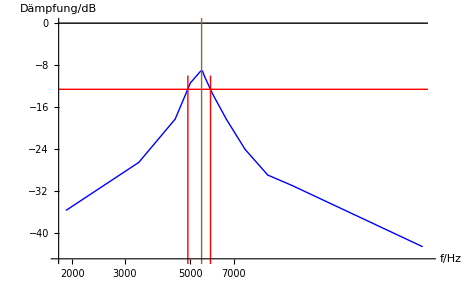

```mathematica
max=0.2/0.5
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}];
p1 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}];
fi3 = Interpolation[Table[{10 Log[At[[x-1,1]]],M[[x,1]]},{x,2,6}],InterpolationOrder->1];
fi4 = Interpolation[Table[{10 Log[At[[x-1,1]]],M[[x,1]]},{x,7,14}],InterpolationOrder->1];
Show[ErrorListLogLinearPlot[p1,Joined-> True,PlotStyle-> {Blue},PlotRange->{{1800,31500},{-45,0}}],
LogLinearPlot[{(*{10Log[1/√2]},*){0},{10Log[max/(√2)]}},{x,1800,31500},PlotStyle-> {Black,Red}],
ListLogLinearPlot[{{5450,-120},{5450,120}},Joined ->True,PlotStyle-> {Brown}],
ListLogLinearPlot[{{fi3[10Log[max/(√2)]],-120},{fi3[10Log[max/(√2)]],-10}},Joined ->True,PlotStyle-> {Red}],
ListLogLinearPlot[{{fi4[10Log[max/(√2)]],-120},{fi4[10Log[max/(√2)]],-10}},Joined ->True,PlotStyle-> {Red}]
(*ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],*)
,AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

```mathematica
fi3[10Log[max/(√2)]]
```

4900.28

### Phasengang

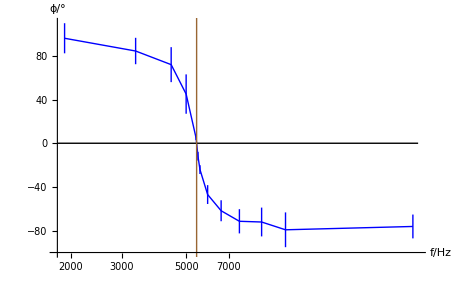

```mathematica
ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}];
p2 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,1]],ϕ[[x-1,2]]]},{x,2,Length[M]}];
fi5 = Interpolation[Table[{ϕ[[x-1,1]],M[[x,1]]},{x,2,10}],InterpolationOrder->1];
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue},PlotRange->{{1800,31500},{-100,110}}],
LogLinearPlot[{{0}},{x,1800,31500},PlotStyle-> {Black}],
ListLogLinearPlot[{{5433.57,-120},{5433.57,120}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel-> {"f/Hz","ϕ/°"}]
```

```mathematica
fi5[0]
```

5433.57

## Amplitudengang und Phasengang der Induktivität

```mathematica
Begin["I`"];
```

### Messung (Achtung! Konstante Eingangsspannung von 2 V Spitze-Spitze, manuell nachregeln!)

```mathematica
{{N, "f/Hz", "Δf/Hz", "Ua/V", "ΔUa/V", "δt", "Δδt"}, {1, 1906, 1, 1.4*2*0.1, 0.02, 1.3*0.2*10^-3, 40*10^-6}, {2, 3349, 1, 3.1*2*0.2, 0.04, 2.8*50*10^-6, 10*10^-6}, {3, 4440, 1, 2.1*2*1, 0.2, 2*50*10^-6, 10*10^-6}, {4, 5000, 1, 2.3*2*2, 0.4, 1.4*50*10^-6, 10*10^-6}, {5, 5410, 1, 3.2*2*2, 0.4, 0.8*50*10^-6, 10*10^-6}, {6, 5491, 1, 3.2*2*2, 0.4, 0.7*50*10^-6, 10*10^-6}, {7, 5580, 1, 2.9*2*2, 0.4, 0.6*50*10^-6, 10*10^-6}, {8, 5.93*10^3, 10, 2.1*2*2, 0.4, 0.4*50*10^-6, 10*10^-6}, {9, 6.60*10^3, 10, 2.7*2*1, 0.2, 0.4*20*10^-6, 4*10^-6}, {10, 7.63*10^3, 10, 2*2*1, 0.2, 0.2*20*10^-6, 4*10^-6}, {11, 9.10*10^3, 10, 1.6*2*1, 0.2, 0.3*10*10^-6, 2*10^-6}, {12, 11.00*10^3, 10, 1.3*2*1, 0.2, 0.4*5*10^-6, 10^-6}, {13, 30.22*10^3, 10, 2.1*2*0.5, 0.1, 0, 10^-6/5}}//TableForm//N
```

N | f/Hz | Δf/Hz | Ua/V | ΔUa/V | δt | Δδt
1. | 1906. | 1. | 0.28 | 0.02 | 0.00026 | 0.00004
2. | 3349. | 1. | 1.24 | 0.04 | 0.00014 | 0.00001
3. | 4440. | 1. | 4.2 | 0.2 | 0.0001 | 0.00001
4. | 5000. | 1. | 9.2 | 0.4 | 0.00007 | 0.00001
5. | 5410. | 1. | 12.8 | 0.4 | 0.00004 | 0.00001
6. | 5491. | 1. | 12.8 | 0.4 | 0.000035 | 0.00001
7. | 5580. | 1. | 11.6 | 0.4 | 0.00003 | 0.00001
8. | 5930. | 10. | 8.4 | 0.4 | 0.00002 | 0.00001
9. | 6600. | 10. | 5.4 | 0.2 | 8.×10^-6 | 4.×10^-6
10. | 7630. | 10. | 4. | 0.2 | 4.×10^-6 | 4.×10^-6
11. | 9100. | 10. | 3.2 | 0.2 | 3.×10^-6 | 2.×10^-6
12. | 11000. | 10. | 2.6 | 0.2 | 2.×10^-6 | 1.×10^-6
13. | 30220. | 10. | 2.1 | 0.1 | 0. | 2.×10^-7

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {1906, 1.4*2*0.1, 1.3*0.2*10^-3, 4*0.5}, {3349, 3.1*2*0.2, 2.8*50*10^-6, 4*0.5}, {4440, 2.1*2*1, 2*50*10^-6, 4*0.5}, {5000, 2.3*2*2, 1.4*50*10^-6, 4*0.5}, {5410, 3.2*2*2, 0.8*50*10^-6, 4*0.5}, {5491, 3.2*2*2, 0.7*50*10^-6, 4*0.5}, {5580, 2.9*2*2, 0.6*50*10^-6, 4*0.5}, {5.93*10^3, 2.1*2*2, 0.4*50*10^-6, 4*0.5}, {6.60*10^3, 2.7*2*1, 0.4*20*10^-6, 4*0.5}, {7.63*10^3, 2*2*1, 0.2*20*10^-6, 4*0.5}, {9.10*10^3, 1.6*2*1, 0.3*10*10^-6, 4*0.5}, {11.00*10^3, 1.3*2*1, 0.4*5*10^-6, 4*0.5}, {30.22*10^3, 2.1*2*0.5, 0, 4*0.5}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {1, 0.02, 40*10^-6, 0.1}, {1, 0.04, 10*10^-6, 0.1}, {1, 0.2, 10*10^-6, 0.1}, {1, 0.4, 10*10^-6, 0.1}, {1, 0.4, 10*10^-6, 0.1}, {1, 0.4, 10*10^-6, 0.1}, {1, 0.4, 10*10^-6, 0.1}, {10, 0.4, 10*10^-6, 0.1}, {10, 0.2, 4*10^-6, 0.1}, {10, 0.2, 4*10^-6, 0.1}, {10, 0.2, 2*10^-6, 0.1}, {10, 0.2, 10^-6, 0.1}, {10, 0.1, 10^-6/5, 0.1}};

Ue=4;(*eff, fluke 175*)
due=0.4;
```

### Amplitudengang

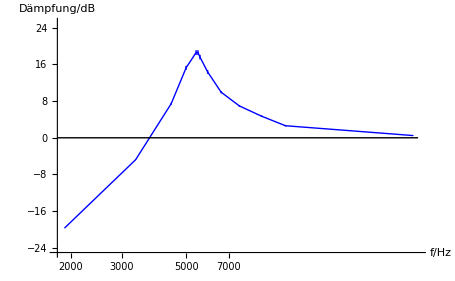

```mathematica
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}];
p2 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}];
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue},PlotRange->{{1800,31500},{-25,25}}],
LogLinearPlot[{(*{10Log[1/√2]},*){0}},{x,1800,31500},PlotStyle-> {Orange,Black}],
(*ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

### Phasengang

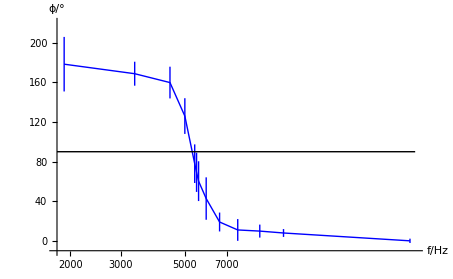

```mathematica
ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}];
p2 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,1]],ϕ[[x-1,2]]]},{x,2,Length[M]}];
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue},PlotRange->{{1800,31500},{-10,220}}],
LogLinearPlot[{{90}},{x,1800,31500},PlotStyle-> {Black}],
(*ListLogLinearPlot[{{9360,-120},{9360,120}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel-> {"f/Hz","ϕ/°"}]
```

```mathematica
End[];
```

## Amplitudengang und Phasengang der Kapazität

```mathematica
Begin["C`"];
```

### Messung (Achtung! Konstante Eingangsspannung von 2 V Spitze-Spitze, manuell nachregeln!)

```mathematica
{{N, "f/Hz", "Δf/Hz", "Ua/V", "ΔUa/V", "δt", "Δδt"}, {1, 1906, 1, 2.4*2*0.5, 0.1, 0, 10^-6/5}, {2, 3349, 1, 3.3*2*0.5, 0.1, -0.3*20*10^-6, 4*10^-6}, {3, 4440, 1, 3.2*2*1, 0.2, -0.6*20*10^-6, 4*10^-6}, {4, 5000, 1, 2.7*2*2, 0.4, -1.3*20*10^-6, 4*10^-6}, {5, 5410, 1, 3.2*2*2, 0.4, -2.4*20*10^-6, 4*10^-6}, {6, 5491, 1, 3*2*2, 0.4, -2.6*20*10^-6, 4*10^-6}, {7, 5580, 1, 2.8*2*2, 0.4, -2.8*20*10^-6, 4*10^-6}, {8, 5.93*10^3, 10, 3.6*2*1, 0.2, -3.2*20*10^-6, 4*10^-6}, {9, 6.60*10^3, 10, 3.7*2*0.5, 0.1, -3.2*20*10^-6, 4*10^-6}, {10, 7.63*10^3, 10, 2*2*0.5, 0.1, -3.0*20*10^-6, 4*10^-6}, {11, 9.10*10^3, 10, 3.8*2*0.2, 0.04, -2.5*20*10^-6, 4*10^-6}, {12, 11.00*10^3, 10, 3.4*2*0.1, 0.02, -2.1*20*10^-6, 4*10^-6}, {13, 30.22*10^3, 10, 2*2*20*10^-3, 4*10^-3, -3*5*10^-6, 10^-6}}//TableForm//N
```

N | f/Hz | Δf/Hz | Ua/V | ΔUa/V | δt | Δδt
1. | 1906. | 1. | 2.4 | 0.1 | 0. | 2.×10^-7
2. | 3349. | 1. | 3.3 | 0.1 | -6.×10^-6 | 4.×10^-6
3. | 4440. | 1. | 6.4 | 0.2 | -0.000012 | 4.×10^-6
4. | 5000. | 1. | 10.8 | 0.4 | -0.000026 | 4.×10^-6
5. | 5410. | 1. | 12.8 | 0.4 | -0.000048 | 4.×10^-6
6. | 5491. | 1. | 12. | 0.4 | -0.000052 | 4.×10^-6
7. | 5580. | 1. | 11.2 | 0.4 | -0.000056 | 4.×10^-6
8. | 5930. | 10. | 7.2 | 0.2 | -0.000064 | 4.×10^-6
9. | 6600. | 10. | 3.7 | 0.1 | -0.000064 | 4.×10^-6
10. | 7630. | 10. | 2. | 0.1 | -0.00006 | 4.×10^-6
11. | 9100. | 10. | 1.52 | 0.04 | -0.00005 | 4.×10^-6
12. | 11000. | 10. | 0.68 | 0.02 | -0.000042 | 4.×10^-6
13. | 30220. | 10. | 0.08 | 0.004 | -0.000015 | 1.×10^-6

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {1906, 2.4*2*0.5, 0, 4*0.5}, {3349, 3.3*2*0.5, -0.3*20*10^-6, 4*0.5}, {4440, 3.2*2*1, -0.6*20*10^-6, 4*0.5}, {5000, 2.7*2*2, -1.3*20*10^-6, 4*0.5}, {5410, 3.2*2*2, -2.4*20*10^-6, 4*0.5}, {5491, 3*2*2, -2.6*20*10^-6, 4*0.5}, {5580, 2.8*2*2, -2.8*20*10^-6, 4*0.5}, {5.93*10^3, 3.6*2*1, -3.2*20*10^-6, 4*0.5}, {6.60*10^3, 3.7*2*0.5, -3.2*20*10^-6, 4*0.5}, {7.63*10^3, 2*2*0.5, -3.0*20*10^-6, 4*0.5}, {9.10*10^3, 3.8*2*0.2, -2.5*20*10^-6, 4*0.5}, {11.00*10^3, 3.4*2*0.1, -2.1*20*10^-6, 4*0.5}, {30.22*10^3, 2*2*20*10^-3, -3*5*10^-6, 4*0.5}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {1, 0.1, 10^-6/5, 0.1}, {1, 0.1, 4*10^-6, 0.1}, {1, 0.2, 4*10^-6, 0.1}, {1, 0.4, 4*10^-6, 0.1}, {1, 0.4, 4*10^-6, 0.1}, {1, 0.4, 4*10^-6, 0.1}, {1, 0.4, 4*10^-6, 0.1}, {10, 0.2, 4*10^-6, 0.1}, {10, 0.1, 4*10^-6, 0.1}, {10, 0.1, 4*10^-6, 0.1}, {10, 0.04, 4*10^-6, 0.1}, {10, 0.02, 4*10^-6, 0.1}, {10, 4*10^-3, 10^-6, 0.1}};

Ue=4;(*eff, fluke 175*)
due=0.4;
```

### Amplitudengang

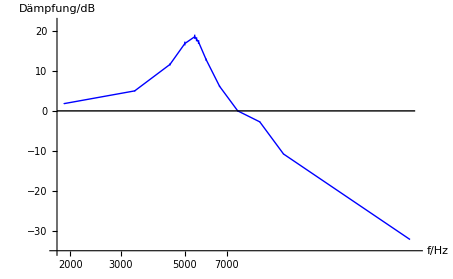

```mathematica
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}];
p3 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}];
Show[ErrorListLogLinearPlot[p3,Joined-> True,PlotStyle-> {Blue},PlotRange->{{1800,31500},{-35,22}}],
LogLinearPlot[{{0}},{x,1800,31500},PlotStyle-> {Orange,Black}],
(*ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

### Phasengang

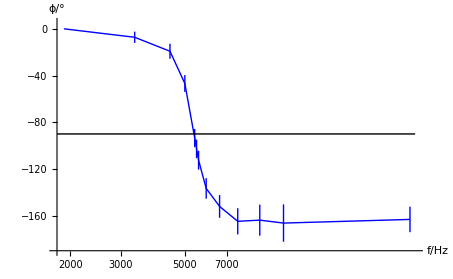

```mathematica
ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}];
p2 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,1]],ϕ[[x-1,2]]]},{x,2,Length[M]}];
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue},PlotRange->{{1800,31500},{-190,5}}],
LogLinearPlot[{{-90}},{x,1800,31500},PlotStyle-> {Black}],
(*ListLogLinearPlot[{{9360,-120},{9360,120}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel-> {"f/Hz","ϕ/°"}]
```

```mathematica
End[];
```

## Amplitudengang Widerstand 50Ω

```mathematica
Begin["R2`"];
```

### Messung (Achtung! Konstante Eingangsspannung von 2 V Spitze-Spitze, manuell nachregeln!)

```mathematica
{{N, "f/Hz", "Δf/Hz", "Ua/V", "ΔUa/V"}, {1, 1906, 1, 2.2*2*50*10^-3, 0.01}, {2, 3349, 1, 2.8*2*0.1, 0.02}, {3, 4440, 1, 2.6*2*0.2, 0.04}, {4, 5000, 1, 3.6*2*0.2, 0.04}, {5, 5410, 1, 3.8*2*0.2, 0.04}, {6, 5491, 1, 3.7*2*0.2, 0.04}, {7, 5580, 1, 3.7*2*0.2, 0.04}, {8, 5.93*10^3, 10, 3.4*2*0.2, 0.04}, {9, 6.60*10^3, 10, 2.4*2*0.2, 0.04}, {10, 7.63*10^3, 10, 3.4*2*0.1, 0.02}, {11, 9.10*10^3, 10, 2.4*2*0.1, 0.02}, {12, 11.00*10^3, 10, 1.8*2*0.1, 0.02}, {13, 30.22*10^3, 10, 2.8*2*50*10^-3, 0.01}}//TableForm
```

N | f/Hz | Δf/Hz | Ua/V | ΔUa/V
1 | 1906 | 1 | 0.22 | 0.01
2 | 3349 | 1 | 0.56 | 0.02
3 | 4440 | 1 | 1.04 | 0.04
4 | 5000 | 1 | 1.44 | 0.04
5 | 5410 | 1 | 1.52 | 0.04
6 | 5491 | 1 | 1.48 | 0.04
7 | 5580 | 1 | 1.48 | 0.04
8 | 5930. | 10 | 1.36 | 0.04
9 | 6600. | 10 | 0.96 | 0.04
10 | 7630. | 10 | 0.68 | 0.02
11 | 9100. | 10 | 0.48 | 0.02
12 | 11000. | 10 | 0.36 | 0.02
13 | 30220. | 10 | 0.28 | 0.01

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {1906, 2.2*2*50*10^-3, □, 4*0.5}, {3349, 2.8*2*0.1, □, 4*0.5}, {4440, 2.6*2*0.2, □, 4*0.5}, {5000, 3.6*2*0.2, □, 4*0.5}, {5410, 3.8*2*0.2, □, 4*0.5}, {5491, 3.7*2*0.2, □, 4*0.5}, {5580, 3.7*2*0.2, □, 4*0.5}, {5.93*10^3, 3.4*2*0.2, □, 4*0.5}, {6.60*10^3, 2.4*2*0.2, □, 4*0.5}, {7.63*10^3, 3.4*2*0.1, □, 4*0.5}, {9.10*10^3, 2.4*2*0.1, □, 4*0.5}, {11.00*10^3, 1.8*2*0.1, □, 4*0.5}, {30.22*10^3, 2.8*2*50*10^-3, □, 4*0.5}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {1, 0.01, □, 0.1}, {1, 0.02, □, 0.1}, {1, 0.04, □, 0.1}, {1, 0.04, □, 0.1}, {1, 0.04, □, 0.1}, {1, 0.04, □, 0.1}, {1, 0.04, □, 0.1}, {10, 0.04, □, 0.1}, {10, 0.04, □, 0.1}, {10, 0.02, □, 0.1}, {10, 0.02, □, 0.1}, {10, 0.02, □, 0.1}, {10, 0.01, □, 0.1}};

Ue=4;(*eff, fluke 175*)
due=0.4;
```

### Amplitudengang

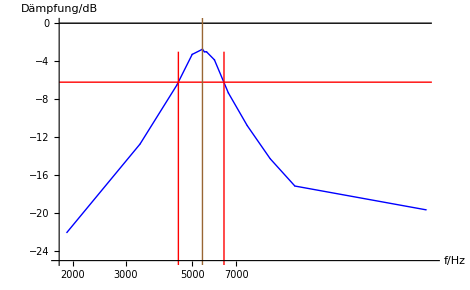

```mathematica
max=3.8*2*0.2/2;
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}];
p4 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}];
fi3 = Interpolation[Table[{10 Log[At[[x-1,1]]],M[[x,1]]},{x,2,6}],InterpolationOrder->1];
fi4 = Interpolation[Table[{10 Log[At[[x-1,1]]],M[[x,1]]},{x,8,14}],InterpolationOrder->1];
Show[ErrorListLogLinearPlot[p4,Joined-> True,PlotStyle-> {Blue},PlotRange->{{1800,31500},{-25,0}}],
LogLinearPlot[{(*{10Log[1/√2]},*){0},{10Log[max/(√2)]}},{x,1800,31500},PlotStyle-> {Black,Red}],
ListLogLinearPlot[{{5410,-120},{5410,120}},Joined ->True,PlotStyle-> {Brown}],
ListLogLinearPlot[{{fi3[10Log[max/(√2)]],-100},{fi3[10Log[max/(√2)]],-3}},Joined ->True,PlotStyle-> {Red}],
ListLogLinearPlot[{{fi4[10Log[max/(√2)]],-100},{fi4[10Log[max/(√2)]],-3}},Joined ->True,PlotStyle-> {Red}],
(*ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],*)
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

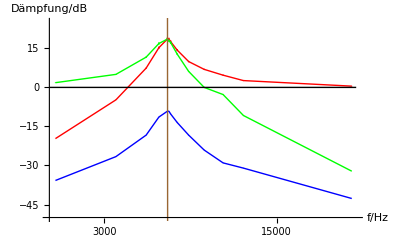

```mathematica
Show[ErrorListLogLinearPlot[{p1,p2,p3},Joined-> True,PlotStyle-> {Blue,Red, Green},PlotRange->{{1800,31500},{-50,25}}],
ListLogLinearPlot[{{5430,-120},{5410,120}},Joined ->True,PlotStyle-> {Brown}],
LogLinearPlot[{{0}},{x,1800,31500},PlotStyle-> {Black}],AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```